```mathematica
Quiet@Remove["`*"]
```

## Constants

```mathematica
angle1=0;
```

```mathematica
angle2=2π;
```

```mathematica
nAngles=55;
```

```mathematica
ΔAngles=(angle2-angle1)/nAngles
```

(2 π)/55

## Graphical Elements

```mathematica
r=0.007;
```

```mathematica
circle=circleArc=Graphics[{Thickness[r],Circle[{0,0},1,{0,2Pi}]}];
```

```mathematica
positionList=Table[Graphics[{Thickness[r],{Arrow[{{0,0},{Cos[θ],Sin[θ]}}]}}],{θ,angle1,angle2,ΔAngles}];
```

```mathematica
velocityList=Table[Graphics[{Thickness[r],Gray,{Arrow[{{Cos[θ],Sin[θ]},{Cos[θ]-Sin[θ],Cos[θ]+Sin[θ]}}]}}],{θ,angle1,angle2,ΔAngles}];
```

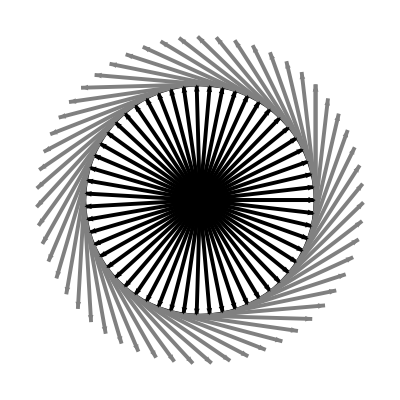

```mathematica
Show[circle,positionList,velocityList]
```